```mathematica
SetDirectory[ToFileName[("FileName"/.NotebookInformation[EvaluationNotebook[]])[[1]],"Data"]];
Clear[AllFiles,FileData1,len1,f];AllFiles=Sort[FileNames["*.csv"]];len1=Length[AllFiles];
For[i=1,i≤len1,i++,{f=Import[AllFiles[[i]]];FileData1[i]=Flatten[Take[f,{1,-1}]],Clear[f]}];
```

```mathematica
(* FileData1[len1+1]=Table[RandomInteger[{1,4}],{i,1,1024}]; len1 = len1+1 *)
```

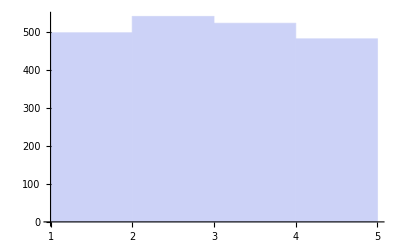
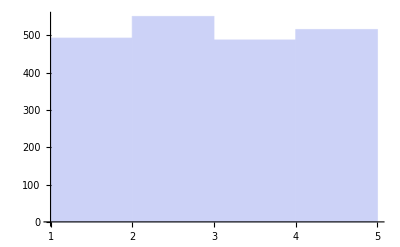
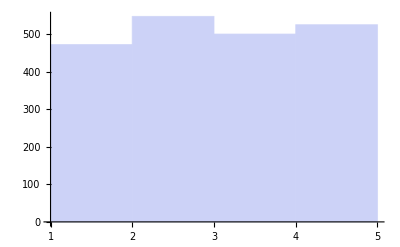
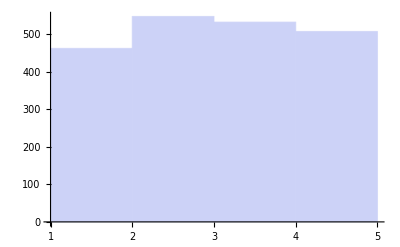
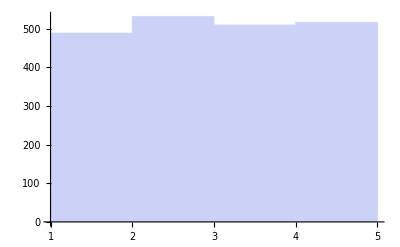
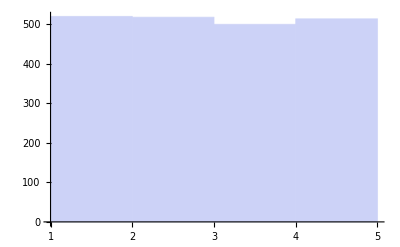
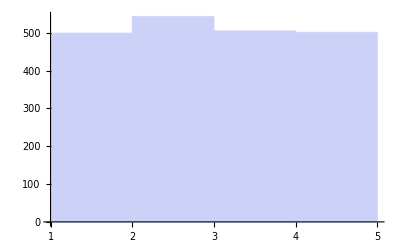
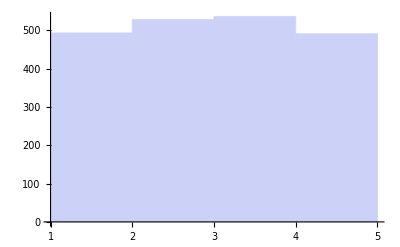

```mathematica
Table[Histogram[FileData1[i]],{i,1,len1}]
```

```mathematica
Vv={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
Y={{0,-ⅈ},{ⅈ,0}};Z={{1,0},{0,-1}};X={{0,1},{1,0}};
```

```mathematica
Orth=Table[Table[({ⅈ^FileData1[m][[k]]}),{k,1,Length[FileData1[m]]}],{m,1,len1}];
```

```mathematica
ZMX1 = Table[If[i == j, If[EvenQ[i], ⅈ, 1], 0], {i, Length[FileData1[2]]}, {j, Length[FileData1[2]]}];Det[ZMX1]
```

1

```mathematica
ZMX2 = Table[If[i == j,(ⅈ^i ),0], {i, Length[FileData1[2]]}, {j, Length[FileData1[2]]}];Det[ZMX2]
```

1

```mathematica
Manipulate[{ConjugateTranspose[Orth[[k]]].ZMX1.Orth[[k]],Median[FileData1[k]]},{k,1,len1,1}]
```

```mathematica
Manipulate[N[Entropy[FileData1[k]]],{k,1,len1,1}]
```

```mathematica
II =DiagonalMatrix[{1,1,1,1}]; II// MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
II[[FileData1[1][[222]]]]
```

{0,0,1,0}

```mathematica
Clear[Data];For[i=1,i<=len1,i++,Data[i]=Transpose[Table[II[[FileData1[i][[k]]]],{k,1,1024}] ]];
```

```mathematica
Clear[V1,V2];For[i=1,i<=len1,i++,{V1[i]=Data[i][[1]]+Data[i][[3]],V2[i]=Data[i][[2]]+Data[i][[4]]}];
```

```mathematica
Manipulate[{N[Entropy[V1[k]]],N[Entropy[V2[k]]]},{k,1,len1,1}]
```

```mathematica
Manipulate[{Entropy[Data[k]]},{k,1,len1,1}]
```

```mathematica
Manipulate[{aa[k]=Table[N[Entropy[Data[k][[i]]]],{i,1,4}],Sum[aa[k][[m]],{m,1,4}]/4},{k,1,len1,1}]
```

```mathematica
Gm5={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};Gm5 //MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
Gm5.II
```

{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}}

```mathematica
BI =DiagonalMatrix[{ⅈ,-1,1,-ⅈ}]; BI// MatrixForm
```

(ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -ⅈ)

```mathematica
Gm2={{0,0,0,-ⅈ},{0,0,ⅈ,0},{0,ⅈ,0,0},{-ⅈ,0,0,0}};Gm2 //MatrixForm
```

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)

```mathematica
Gm2.BI //MatrixForm
```

(0 | 0 | 0 | -1
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0)

```mathematica
Gm2={{0,0,0,-ⅈ},{0,0,ⅈ,0},{0,ⅈ,0,0},{-ⅈ,0,0,0}};Gm2 //MatrixForm
```

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)

```mathematica
Det[Gm2.BI]
```

-1

```mathematica
Sum[Flatten[Orth][[i]],{i,1,2048}]
```

-59-25 ⅈ

```mathematica
DT[1]=KroneckerProduct[Data[1][[1]],Data[1][[2]]];{Det[DT[1]],Tr[DT[1]]}
```

{0,0}

```mathematica
Sum[Sum[Data[1][[k]][[i]],{i,1,1024}],{k,1,4}]
```

1024

```mathematica
ll=Gm2.Data[1];Sum[Sum[ll[[k]][[i]],{i,1,1024}],{k,1,4}]
```

60 ⅈ